# ЛАБОРАТОРНАЯ РАБОТА 2. СТРУКТУРА ВЫРАЖЕНИЯ

Выполнил студент ММФ БГУ
КМ, 1 к, 5 гр. Плисюк Г.С.
15 сентября 2021
Вариант 9

## 1. Построение дерева выражения

### Задание 1.1

Введите два математических выражения, каждое — в отдельную вычисляемую ячейку: выражение (1.1) и Ваш вариант из предложенной ниже таблицы. Используйте возможности двумерного ввода.

```mathematica
-1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7π x z+z^(6x)
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)

```mathematica
ⅇ^(a x) Cos[b x]^2
```

ⅇ^(a x) Cos[b x]^2

π - EscpiEsc, ∞ - EscinfEsc, ⅇ - EsceeEsc, ⅈ - EsciiEsc.

Superscript - Ctrl+6, Fraction - Ctrl+/, Radical - Ctrl+2.

### Задание 1.2

Постройте в тетради, на бумаге, два дерева: выражения (1.1) и выражения Вашего варианта, по аналогии с деревом выражения, представленным на рис. 2.1.

```mathematica
(1-2 ⅈ)/(2 y-0.1 x)+z^(4 x)-1/3//FullForm
```

Plus[Rational[-1,3],Times[Complex[1,-2],Power[Plus[Times[-0.1,x],Times[2,y]],-1]],Power[z,Times[4,x]]]

Дерево выражения выстраивается с использованием заголовков функций в качестве узлов дерева и её аргументов в качестве ветвей с сохранением структуры уровней.

```mathematica
expr1 = -1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7π x z+z^(6x)
?expr1
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)

```mathematica
myExpr = ⅇ^(a x) Cos[b x]^2
?myExpr
```

ⅇ^(a x) Cos[b x]^2

```mathematica
expr1//FullForm
```

Plus[Rational[-1,5],E,Times[Complex[1,-2],Power[Plus[Times[-0.4,x],Times[3,y]],-1]],Times[-7,Pi,x,z],Power[z,Times[6,x]]]

```mathematica
myExpr//FullForm
```

Times[Power[E,Times[a,x]],Power[Cos[Times[b,x]],2]]

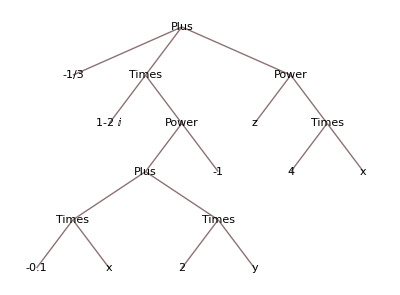

```mathematica
(1-2 ⅈ)/(2 y-0.1 x)+z^(4 x)-1/3//TreeForm
```

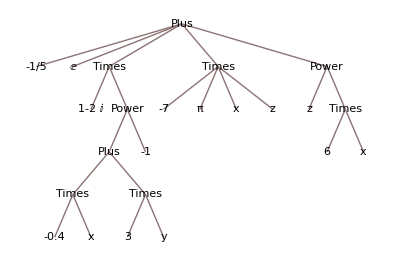

```mathematica
expr1//TreeForm
```

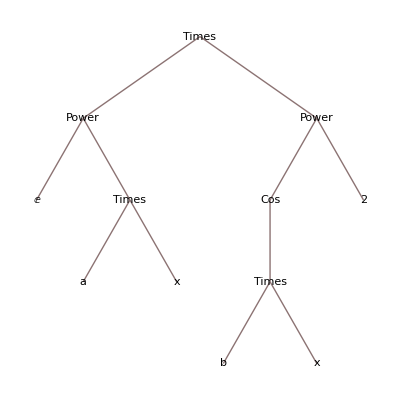

```mathematica
myExpr//TreeForm
```

Деревья выражения с рис. 2.1 и построенное встроенной функцией TreeForm отличаются только внешним видом: у функции ExprAsTree стоит выравнивание по правому краю и узлы дерева с названиями функций и с атомарными выражениями отличаются по цвету, а у функции TreeForm все ячейки одинаковые и выравнены по центру. Структура деревьев, построенных двумя функциями, не отличается.

## 2. Анализ структуры выражения

### Задание 2.1

Изучите возможности исследования структуры выражения посредством функций Level, Depth. Используйте в качестве примеров выражение (1.1) и выражение Вашего варианта.

```mathematica
expr1 = -1/5+ⅇ+(1-2ⅈ)/(-.4x+3y)-7π x z+z^(6x)
?expr1
```

-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)

```mathematica
myExpr = ⅇ^(a x) Cos[b x]^2
?myExpr
```

ⅇ^(a x) Cos[b x]^2

```mathematica
expr1//TreeForm
```

-Graphics-

```mathematica
myExpr//TreeForm
```

-Graphics-

```mathematica
Level[expr1,{1}]
```

{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),-7 π x z,z^(6 x)}

```mathematica
Level[expr1,{2}]
```

{1-2 ⅈ,1/(-0.4 x+3 y),-7,π,x,z,z,6 x}

```mathematica
Level[expr1,{3}]
```

{-0.4 x+3 y,-1,6,x}

```mathematica
Level[expr1,{4}]
```

{-0.4 x,3 y}

```mathematica
Level[expr1,{5}]
```

{-0.4,x,3,y}

0-ой уровень любого выражения, в том числе и expr1, соответствует всему выражению.
	Функция Level возвращает список, т. е. выражение с головой List.

```mathematica
Depth[expr1]
```

6

Значение выражения Depth равно количеству уровней.
	Так как нумерация уровней начинается с 0, то номер последнего уровня произвольного выражения expr выражается как Depth[expr]-1.

```mathematica
Level[expr1,{5}]
```

{-0.4,x,3,y}

```mathematica
Level[expr1,{6}]
```

{}

Максимальное натуральное число n, при котором вычисленное выражение Level[expr1,{n}] возвращает непустой список - 5. Это число на единицу меньше значения выражения Depth[expr1].

```mathematica
Level[expr1, {-1}]
```

{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,-7,π,x,z,z,6,x}

```mathematica
Level[expr1, {-2}]
```

{-0.4 x,3 y,-7 π x z,6 x}

```mathematica
Level[expr1,{Depth[expr1]-1}]
Level[expr1,{−1}]
```

{-0.4,x,3,y}

{-1/5,ⅇ,1-2 ⅈ,-0.4,x,3,y,-1,-7,π,x,z,z,6,x}

```mathematica
Level[expr1,{Depth[expr1]-2}]
Level[expr1,{−2}]
```

{-0.4 x,3 y}

{-0.4 x,3 y,-7 π x z,6 x}

Выражение вида Level[expr1,{Depth[expr1]-n}] возвращает список подвыражений, находящихся на n-1 уровень выше последнего уровня, а выражение вида Level[expr1,{-n}] возвращает список всех подвыражений с глубиной n.

### Задание 2.2

Форматируйте структуру выражения (1.1), используя функции Head, Table, MatrixForm. Используйте чистые (анонимные, безымянные) функции и функцию Map.

```mathematica
Table[Level[expr1,{i}],{i,0, Depth[expr1]-1}]
```

{{-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)},{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),-7 π x z,z^(6 x)},{1-2 ⅈ,1/(-0.4 x+3 y),-7,π,x,z,z,6 x},{-0.4 x+3 y,-1,6,x},{-0.4 x,3 y},{-0.4,x,3,y}}

```mathematica
Table[Level[expr1,{i}],{i,0, Depth[expr1]-1}]//MatrixForm
```

({-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x)}
{-1/5,ⅇ,(1-2 ⅈ)/(-0.4 x+3 y),-7 π x z,z^(6 x)}
{1-2 ⅈ,1/(-0.4 x+3 y),-7,π,x,z,z,6 x}
{-0.4 x+3 y,-1,6,x}
{-0.4 x,3 y}
{-0.4,x,3,y})

```mathematica
Head/@Level[expr1,{0}]
```

{Plus}

```mathematica
Head/@Level[expr1,{1}]
```

{Rational,Symbol,Times,Times,Power}

```mathematica
Head/@Level[expr1,{2}]
```

{Complex,Power,Integer,Symbol,Symbol,Symbol,Symbol,Times}

```mathematica
Head/@Level[expr1,{3}]
```

{Plus,Integer,Integer,Symbol}

```mathematica
Head/@Level[expr1,{4}]
```

{Times,Times}

```mathematica
Head/@Level[expr1,{5}]
```

{Real,Symbol,Integer,Symbol}

```mathematica
Table[Head/@Level[expr1,{i}],{i,0, Depth[expr1]-1}]
```

{{Plus},{Rational,Symbol,Times,Times,Power},{Complex,Power,Integer,Symbol,Symbol,Symbol,Symbol,Times},{Plus,Integer,Integer,Symbol},{Times,Times},{Real,Symbol,Integer,Symbol}}

```mathematica
Table[Head/@Level[expr1,{i}],{i,0, Depth[expr1]-1}]//MatrixForm
```

({Plus}
{Rational,Symbol,Times,Times,Power}
{Complex,Power,Integer,Symbol,Symbol,Symbol,Symbol,Times}
{Plus,Integer,Integer,Symbol}
{Times,Times}
{Real,Symbol,Integer,Symbol})

```mathematica
{Head[#],#}&/@Level[expr1,{1}]
```

{{Rational,-1/5},{Symbol,ⅇ},{Times,(1-2 ⅈ)/(-0.4 x+3 y)},{Times,-7 π x z},{Power,z^(6 x)}}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{0}]
```

{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x))}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{1}]
```

{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{2}]
```

{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{3}]
```

{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{4}]
```

{(Times
-0.4 x),(Times
3 y)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[expr1,{5}]
```

{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

```mathematica
Table[MatrixForm[{Head[#],#}]&/@Level[expr1,{i}],{i,0, Depth[expr1]-1}]
```

{{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x))},{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))},{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)},{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)},{(Times
-0.4 x),(Times
3 y)},{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}}

### Задание 2.3

Изучите возможности исследования структуры выражения посредством функций AtomQ, Position, Part, Take, Length. Используйте выражение (1.1) в качестве примера.

```mathematica
Position[expr1, x]
```

{{3,2,1,1,2},{4,3},{5,2,2}}

```mathematica
Position[expr1, y]
```

{{3,2,1,2,2}}

```mathematica
Position[expr1, z]
```

{{4,4},{5,1}}

```mathematica
expr1⟦Length[expr1]-1;;Length[expr1]⟧
```

-7 π x z+z^(6 x)

```mathematica
Level[expr1,{2}]⟦-2⟧
```

z

```mathematica
Take[expr1, Length[expr1]-1;;Length[expr1]]
```

-7 π x z+z^(6 x)

```mathematica
Take[Level[expr1,{2}],{-2}]
```

{z}

```mathematica
First@Take[Level[expr1,{2}],{-2}]
```

z

```mathematica
AtomQ/@Level[expr1,{1}]
```

{True,True,False,False,False}

```mathematica
AtomQ/@Level[expr1,{2}]
```

{True,False,True,True,True,True,True,False}

Функция AtomQ позволяет определить, является ли выражение (подвыражение выражения) атомарным объектом.
	Функция Position позволяет определить все позиции, на которых подвыражение встречается в выражении.
	Функция Part позволяет извлечь подвыражения выражения, находящиеся на определённых позициях, с оригинальной головой.
	Функция Take позволяет извлечь подвыражения выражения, находящиеся на определённых позициях и представленные в виде списка.
	Функция Length позволяет определить количество аргументов выражения или количество элементов списка.

## 3. Разложение выражения по уровням

### Задание 3.1

Создайте функцию myExprLevels[expr], возвращающую произвольное выражение expr в виде подвыражений, разложенных по уровням. Для каждого уровня выражения expr функция myExprLevels отображает подвыражения, которые находятся на указанном уровне, а также головы этих подвыражений.

```mathematica
myExprLevels[expr_]:=Do[Print[i,":",MatrixForm[{Head[#],#}]&/@Level[expr,{i}]],{i,0, Depth[expr]-1}]
```

```mathematica
myExprLevels[expr1]
```

0:{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x))}

1:{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))}

2:{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)}

3:{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

4:{(Times
-0.4 x),(Times
3 y)}

5:{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

### Задание 3.2

Разложите выражение (1.1) по уровням, используя функцию myExprLevels, построенную ранее. Определите позицию каждого атомарного объекта выражения (1.1). Результаты оформите в виде таблицы.

```mathematica
myExprLevels[expr1]
```

0:{(Plus
-1/5+ⅇ+(1-2 ⅈ)/(-0.4 x+3 y)-7 π x z+z^(6 x))}

1:{(Rational
-1/5),(Symbol
ⅇ),(Times
(1-2 ⅈ)/(-0.4 x+3 y)),(Times
-7 π x z),(Power
z^(6 x))}

2:{(Complex
1-2 ⅈ),(Power
1/(-0.4 x+3 y)),(Integer
-7),(Symbol
π),(Symbol
x),(Symbol
z),(Symbol
z),(Times
6 x)}

3:{(Plus
-0.4 x+3 y),(Integer
-1),(Integer
6),(Symbol
x)}

4:{(Times
-0.4 x),(Times
3 y)}

5:{(Real
-0.4),(Symbol
x),(Integer
3),(Symbol
y)}

```mathematica
GridOfAtoms[expr_]:=Grid[{#,Position[expr,#]}&/@({Select[Level[expr,{-1}],NumericQ],Select[Apply[List,#]&/@Select[List@@Plus@@Level[expr,{-1}], Not[NumericQ[#]]&]//Flatten, Not[NumericQ[#]]&]}//Flatten),Frame->All]
```

```mathematica
GridOfAtoms[expr1]
```

-1/5 | {{1}}
ⅇ | {{2}}
1-2 ⅈ | {{3,1}}
-0.4 | {{3,2,1,1,1}}
3 | {{3,2,1,2,1}}
-1 | {{3,2,2}}
-7 | {{4,1}}
π | {{4,2}}
6 | {{5,2,1}}
x | {{3,2,1,1,2},{4,3},{5,2,2}}
y | {{3,2,1,2,2}}
z | {{4,4},{5,1}}

## 4. Анализ моего выражения, вариант 9

### Задание 4

Выполните пошагово каждое из заданий 2.1 - 3.2, используя в качестве примера выражение Вашего варианта.

```mathematica
myExpr = ⅇ^(a x) Cos[b x]^2
?myExpr
```

ⅇ^(a x) Cos[b x]^2

```mathematica
myExpr//TreeForm
```

-Graphics-

```mathematica
Level[myExpr,{1}]
```

{ⅇ^(a x),Cos[b x]^2}

```mathematica
Level[myExpr,{2}]
```

{ⅇ,a x,Cos[b x],2}

```mathematica
Level[myExpr,{3}]
```

{a,x,b x}

```mathematica
Level[myExpr,{4}]
```

{b,x}

```mathematica
Level[myExpr,{5}]
```

{}

```mathematica
Depth[myExpr]
```

5

Максимальное натуральное число n, при котором вычисленное выражение Level[myExpr,{n}] возвращает непустой список - 4. Это число на единицу меньше значения выражения Depth[myExpr].

```mathematica
Level[myExpr, {-1}]
```

{ⅇ,a,x,b,x,2}

```mathematica
Level[myExpr, {-2}]
```

{a x,b x}

```mathematica
Level[myExpr,{Depth[myExpr]-1}]
Level[myExpr,{−1}]
```

{b,x}

{ⅇ,a,x,b,x,2}

```mathematica
Level[myExpr,{Depth[myExpr]-2}]
Level[myExpr,{−2}]
```

{a,x,b x}

{a x,b x}

```mathematica
Table[Level[myExpr,{i}],{i,0, Depth[myExpr]-1}]
```

{{ⅇ^(a x) Cos[b x]^2},{ⅇ^(a x),Cos[b x]^2},{ⅇ,a x,Cos[b x],2},{a,x,b x},{b,x}}

```mathematica
Table[Level[myExpr,{i}],{i,0, Depth[myExpr]-1}]//MatrixForm
```

({ⅇ^(a x) Cos[b x]^2}
{ⅇ^(a x),Cos[b x]^2}
{ⅇ,a x,Cos[b x],2}
{a,x,b x}
{b,x})

```mathematica
Head/@Level[myExpr,{0}]
```

{Times}

```mathematica
Head/@Level[myExpr,{1}]
```

{Power,Power}

```mathematica
Head/@Level[myExpr,{2}]
```

{Symbol,Times,Cos,Integer}

```mathematica
Head/@Level[myExpr,{3}]
```

{Symbol,Symbol,Times}

```mathematica
Head/@Level[myExpr,{4}]
```

{Symbol,Symbol}

```mathematica
Table[Head/@Level[myExpr,{i}],{i,0, Depth[myExpr]-1}]
```

{{Times},{Power,Power},{Symbol,Times,Cos,Integer},{Symbol,Symbol,Times},{Symbol,Symbol}}

```mathematica
Table[Head/@Level[myExpr,{i}],{i,0, Depth[myExpr]-1}]//MatrixForm
```

({Times}
{Power,Power}
{Symbol,Times,Cos,Integer}
{Symbol,Symbol,Times}
{Symbol,Symbol})

```mathematica
{Head[#],#}&/@Level[myExpr,{1}]
```

{{Power,ⅇ^(a x)},{Power,Cos[b x]^2}}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[myExpr,{0}]
```

{(Times
ⅇ^(a x) Cos[b x]^2)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[myExpr,{1}]
```

{(Power
ⅇ^(a x)),(Power
Cos[b x]^2)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[myExpr,{2}]
```

{(Symbol
ⅇ),(Times
a x),(Cos
Cos[b x]),(Integer
2)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[myExpr,{3}]
```

{(Symbol
a),(Symbol
x),(Times
b x)}

```mathematica
MatrixForm[{Head[#],#}]&/@Level[myExpr,{4}]
```

{(Symbol
b),(Symbol
x)}

```mathematica
Table[MatrixForm[{Head[#],#}]&/@Level[myExpr,{i}],{i,0, Depth[myExpr]-1}]
```

{{(Times
ⅇ^(a x) Cos[b x]^2)},{(Power
ⅇ^(a x)),(Power
Cos[b x]^2)},{(Symbol
ⅇ),(Times
a x),(Cos
Cos[b x]),(Integer
2)},{(Symbol
a),(Symbol
x),(Times
b x)},{(Symbol
b),(Symbol
x)}}

```mathematica
Position[myExpr, x]
```

{{1,2,2},{2,1,1,2}}

```mathematica
Position[myExpr, y]
```

{}

```mathematica
Position[myExpr, z]
```

{}

```mathematica
myExpr⟦Length[myExpr]-1;;Length[myExpr]⟧
```

ⅇ^(a x) Cos[b x]^2

```mathematica
Level[myExpr,{2}]⟦-2⟧
```

Cos[b x]

```mathematica
Take[myExpr, Length[myExpr]-1;;Length[myExpr]]
```

ⅇ^(a x) Cos[b x]^2

```mathematica
Take[Level[myExpr,{2}],{-2}]
```

{Cos[b x]}

```mathematica
First@Take[Level[myExpr,{2}],{-2}]
```

Cos[b x]

```mathematica
AtomQ/@Level[myExpr,{1}]
```

{False,False}

```mathematica
AtomQ/@Level[myExpr,{2}]
```

{True,False,False,True}

```mathematica
myExprLevels[myExpr]
```

0:{(Times
ⅇ^(a x) Cos[b x]^2)}

1:{(Power
ⅇ^(a x)),(Power
Cos[b x]^2)}

2:{(Symbol
ⅇ),(Times
a x),(Cos
Cos[b x]),(Integer
2)}

3:{(Symbol
a),(Symbol
x),(Times
b x)}

4:{(Symbol
b),(Symbol
x)}

```mathematica
GridOfAtoms[myExpr]
```

ⅇ | {{1,1}}
2 | {{2,2}}
a | {{1,2,1}}
b | {{2,1,1,1}}
x | {{1,2,2},{2,1,1,2}}